# Mixed Mode: Cross and R1 mode

#### Animation of the mixed polarization mode of gravitational waves in f(R) theories. The notebook generates the corresponding deformation patterns of a ring of test particles and associated animation via the geodesic deviation equation.

```mathematica
$Assumptions ={x ∈ Reals, y ∈ Reals, z ∈ Reals, t ∈ Reals, α ∈ Reals, ω ∈ Reals,hr ∈ Reals,S10 ∈ Reals, S20 ∈ Reals, θ ∈ Reals,a1∈ Reals,a2∈ Reals,b1∈ Reals,b2∈ Reals}
```

{x∈ℝ,y∈ℝ,z∈ℝ,t∈ℝ,α∈ℝ,ω∈ℝ,hr∈ℝ,S10∈ℝ,S20∈ℝ,θ∈ℝ,a1∈ℝ,a2∈ℝ,b1∈ℝ,b2∈ℝ}

```mathematica
n=4; var= {x,y,z,t};k={0,0,ω,ω};q={0,0,α, α};
```

```mathematica
Do[η[i,j] = If[i == j, 1, 0],{i,1,n},{j,1,n}]; η[4,4] = -1; eta = Table[η[i,j],{i,1,n},{j,1,n}];
```

```mathematica
ηm=Table[η[i,j],{i,1,n},{j,1,n}];ηma=MatrixForm[ηm]; Print[Style["η_μν = ", 18], Style[ηma, 18]];
```

η_μν = (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

## Geodesic deviation equation for hp = 0, hc y R1 non zero.

```mathematica
eqS1= D[S1[z,t],t,t]  -  1/2 S2[z,t] D[hc Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]],t,t]+1/(6 μ^2)S1[z,t]D[R1 Exp[ⅈ Sum[η[i,j] q[[i]] var[[j]],{i,1,4},{j,1,4}]],t,t  ] ;
eqS2= D[S2[z,t],t,t] - 1/2 S1[z,t] D[hc Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]],t,t] +1/(6 μ^2)S2[z,t]D[R1 Exp[ⅈ Sum[η[i,j] q[[i]] var[[j]],{i,1,4},{j,1,4}]],t,t  ] ;
```

```mathematica
S1[z_,t_] = a1/2 S10 +b1/(2 √2)hr Exp[ⅈ Sum[η[i,j] q[[i]] var[[j]],{i,1,4},{j,1,4}]] S10 +(b1 -a1/2)S20-  (ⅈ b2)/(2 √2)hr Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]] S20;
S2[z_,t_] = a2/2 S20 +b2/(2 √2)hr Exp[ⅈ Sum[η[i,j] q[[i]] var[[j]],{i,1,4},{j,1,4}]] S20 + (b2 - a2/2)S10 - (ⅈ b1)/(2 √2)hr Exp[ⅈ Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]]S10;
```

```mathematica
eqS1hr=eqS1 /. {R1->- (3 μ^2)/(√2)hr,hc-> -(ⅈ hr)/(√2)};
eqS2hr=eqS2 /. {R1-> - (3 μ^2)/(√2)hr,hc-> -(ⅈ hr)/(√2)};
```

```mathematica
CoefficientList[%,hr];
```

```mathematica
eqS1fo=CoefficientList[eqS1 /. {R1->- (3 μ^2)/(√2)hr,hc-> -(ⅈ hr)/(√2)},hr][[1]] hr==0
```

True

```mathematica
eqS2fo=CoefficientList[eqS2 /. {R1->- (3 μ^2)/(√2)hr,hc-> -(ⅈ hr)/(√2)},hr][[1]]==0
```

True

```mathematica
Simplify[eqS1fo]
Simplify[eqS2fo]
```

True

True

```mathematica
values2={hr-> 1,S10-> 1,S20->1,ω->1,a1-> 10, a2-> 10, b1-> 1,b2->1, α->3}
```

{hr→1,S10→1,S20→1,ω→1,a1→10,a2→10,b1→1,b2→1,α→3}

```mathematica
{hr->1,S10->1,S20->1,ω->1,a1->10,a2->10,b1->1,b2->1,α->3}
```

{hr→1,S10→1,S20→1,ω→1,a1→10,a2→10,b1→1,b2→1,α→3}

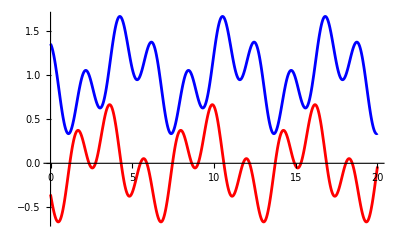

```mathematica
Plot[{Re[S1[0,t]/.values2] ,Im[S2[0,t]/.values2 ]},{t,0,20}, PlotStyle->{Blue,Red},PlotRange->All]
```

```mathematica
values1={hr-> 1,ω->1, α->1}
```

{hr→1,ω→1,α→1}

```mathematica
S1[0,0]
S2[0,0]
```

(a1 S10)/2+(b1 hr S10)/(2 √2)+(-a1/2+b1) S20-(ⅈ b2 hr S20)/(2 √2)

(-a2/2+b2) S10-(ⅈ b1 hr S10)/(2 √2)+(a2 S20)/2+(b2 hr S20)/(2 √2)

```mathematica
solgen=  Extract[Solve[{(a1 S10)/2+(b1 hr S10)/(2 √2)==  Cos[θ],(a2 S20)/2+(b2 hr S20)/(2 √2)==2Sin[θ]},{S10,S20}, Assumptions->{a1∈ Reals,a2∈ Reals,b1∈ Reals,b2∈ Reals}],1]
```

{S10→(4 Cos[θ])/(2 a1+√2 b1 hr),S20→(8 Sin[θ])/(2 a2+√2 b2 hr)}

```mathematica
values3={hr-> 0.5,ω->1,α->2,a1-> -1, a2->1, b1-> 1,b2->1};
```

```mathematica
{Re[S1[0,tfin]/.solgen/. values3],Re[S2[0,tfin]/. solgen/.values3]}
```

{Re[(1.67317+0.532146 ⅈ) Cos[θ]+(4.02295-0.323968 ⅈ) Sin[θ]],Re[(-1.11787+0.339168 ⅈ) Cos[θ]+(1.357-0.508298 ⅈ) Sin[θ]]}

```mathematica
Do[points[θ][t_]= {-Re[S1[0,t]/. solgen /. values3],Re[S2[0,t]/.solgen/.values3]},{θ,0,2π,π/4}];
```

#### Dots Style

```mathematica
Animator[Dynamic[tfin],{0,20}, AnimationRate->1, AnimationRunning->False,AppearanceElements->All]
```

```mathematica
Dynamic[Show[Graphics[{PointSize[Medium],Black,Point[{0,0}]},PlotRangePadding-> 1,PlotRange->{{-6,6},{-6,6}}(*,Axes -> True*)],Table[Graphics[{PointSize[Large],Purple,Point[points[θ][tfin]]}],{θ,0,2π,π/4}],Axes->True,AxesLabel->{"S1","S2"}] ]
```

#### GIF Download

```mathematica
(*Rango de tiempo para la animación*)tmax=10;
dt=0.1;

(*Generar frames de la animación*)
frames=Table[Show[Graphics[{PointSize[Medium],Black,Point[{0,0}]},PlotRangePadding->1,PlotRange->{{-6,6},{-6,6}}],Table[Graphics[{PointSize[Large],Purple,Point[points[θ][t]]}],{θ,0,2 Pi,Pi/4}],Axes->True,AxesLabel->{"S1","S2"},ImageSize->400],{t,0,tmax,dt}];

(*Exportar como GIF*)
Export["\\Users\\cindy\\OneDrive/Desktop/breathingcross_dots.gif",frames,"GIF"]
```

\Users\cindy\OneDrive/Desktop/breathingcross_dots.gif

#### Line Style

```mathematica
Animator[Dynamic[tfin],{0,20}, AnimationRate->1, AnimationRunning->False,AppearanceElements->All]
```

```mathematica
Dynamic[ParametricPlot[{Re[-S1[0,tfin]/.solgen/. values3],Re[S2[0,tfin]/. solgen/.values3] },{θ,0,2π},PlotRangePadding-> 1,PlotRange->{{-6,6},{-6,6}},Axes->True,AxesLabel->{S1, S2}, GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed], PlotStyle->Purple]]
```

#### GIF Download

```mathematica
frames=Table[ParametricPlot[{Re[-S1[0,t]/. solgen/. values3],Re[S2[0,t]/. solgen/. values3]},{θ,0,2 π},PlotRange->{{-6,6},{-6,6}},Axes->True,AxesLabel->{"S1","S2"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotStyle->Purple,PlotLabel->Style["Breathing Cross Mode "<>ToString[NumberForm[t,{3,2}]],14,Bold,Black],ImageSize->400],{t,0,10,0.05}];

Export["\\Users\\cindy\\OneDrive/Desktop/breathingcross.gif",frames,"DisplayDurations"->0.03];
```